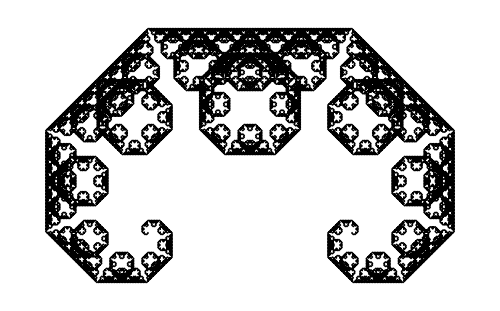

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(x2-x1)/2-(y2-y1)/2,y1+(x2-x1)/2+(y2-y1)/2}};

a2[a_]:=Most[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a]];

list=Nest[a2,{{0.,0.},{1.,0.}},15];

Graphics[Line[list],ImageSize->500]
```

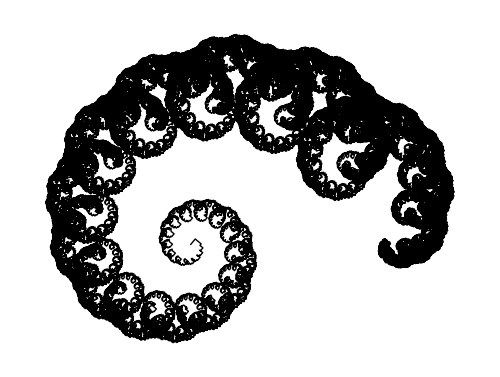

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:=If[(x2-x1)^2+(y2-y1)^2<0.00001,{},{{x1,y1},{x1+4 (x2-x1)/5-2 (y2-y1)/5,y1+2 (x2-x1)/5+4 (y2-y1)/5}}];

a2[a_]:=Most[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a]];

list=Nest[a2,{{0.,0.},{1.,0.}},29];

Graphics[Line[list],ImageSize->500]
```

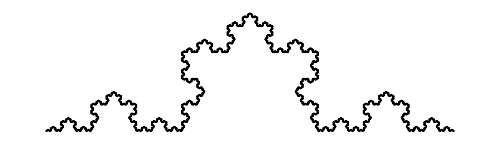

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(x2-x1)/3,y1+(y2-y1)/3},{x1+(x2-x1)/2-Sqrt[3] (y2-y1)/6,y1+Sqrt[3] (x2-x1)/6+(y2-y1)/2},{x1+2 (x2-x1)/3,y1+2 (y2-y1)/3}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-3];

list=Nest[a2,{{0.,0.},{1.,0.}},7];

Graphics[Line[list],ImageSize->500]
```

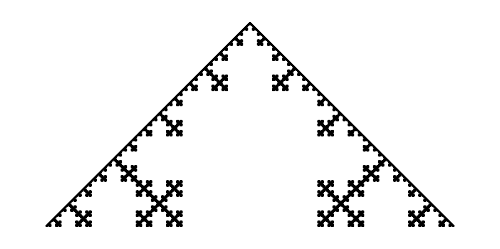

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(x2-x1)/3,y1+(y2-y1)/3},{x1+(x2-x1)/3-(y2-y1)/3,y1+(x2-x1)/3+(y2-y1)/3},{x1+2 (x2-x1)/3-(y2-y1)/3,y1+(x2-x1)/3+2 (y2-y1)/3},{x1+2 (x2-x1)/3,y1+2 (y2-y1)/3}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-4];

list=Nest[a2,{{0.,0.},{1.,0.}},6];

Graphics[Line[list],ImageSize->500]
```

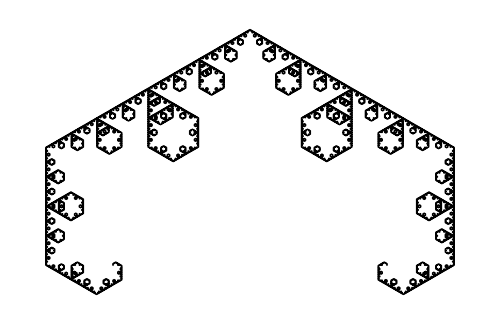

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(x2-x1)/4-Sqrt[3] (y2-y1)/4,y1+Sqrt[3] (x2-x1)/4+(y2-y1)/4},{x1+3 (x2-x1)/4-Sqrt[3] (y2-y1)/4,y1+Sqrt[3] (x2-x1)/4+3 (y2-y1)/4}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-2];

list=Nest[a2,{{0.,0.},{1.,0.}},9];

Graphics[Line[list],ImageSize->500]
```

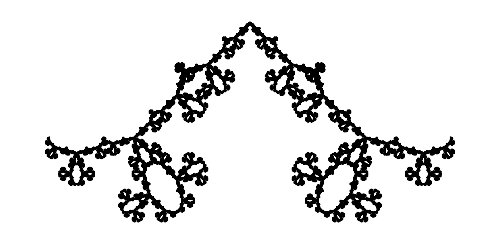

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(3-Sqrt[3]) (x2-x1)/4+(Sqrt[3]-1) (y2-y1)/4,y1-(Sqrt[3]-1) (x2-x1)/4+(3-Sqrt[3]) (y2-y1)/4},{x1+(3-Sqrt[3]) (x2-x1)/4-(Sqrt[3]-1) (y2-y1)/4,y1+(Sqrt[3]-1) (x2-x1)/4+(3-Sqrt[3]) (y2-y1)/4},{x1+(1+Sqrt[3]) (x2-x1)/4-(Sqrt[3]-1) (y2-y1)/4,y1+(Sqrt[3]-1) (x2-x1)/4+(1+Sqrt[3]) (y2-y1)/4},{x1+(1+Sqrt[3]) (x2-x1)/4+(Sqrt[3]-1) (y2-y1)/4,y1-(Sqrt[3]-1) (x2-x1)/4+(1+Sqrt[3]) (y2-y1)/4}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-4];

list=Nest[a2,{{0.,0.},{1.,0.}},7];

Graphics[Line[list],ImageSize->500]
```

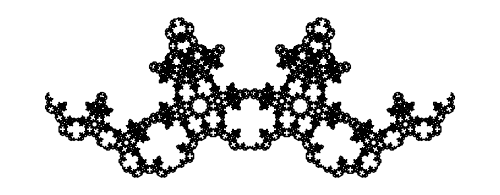

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(3-Sqrt[3]) (x2-x1)/4+(Sqrt[3]-1) (y2-y1)/4,y1-(Sqrt[3]-1) (x2-x1)/4+(3-Sqrt[3]) (y2-y1)/4},{x1+(3-Sqrt[3]) (x2-x1)/4-(Sqrt[3]-1) (y2-y1)/4,y1+(Sqrt[3]-1) (x2-x1)/4+(3-Sqrt[3]) (y2-y1)/4},{x1+(x2-x1)/2+(2-Sqrt[3]) (y2-y1)/2,y1-(2-Sqrt[3]) (x2-x1)/2+(y2-y1)/2},{x1+(1+Sqrt[3]) (x2-x1)/4-(Sqrt[3]-1) (y2-y1)/4,y1+(Sqrt[3]-1) (x2-x1)/4+(1+Sqrt[3]) (y2-y1)/4},{x1+(1+Sqrt[3]) (x2-x1)/4+(Sqrt[3]-1) (y2-y1)/4,y1-(Sqrt[3]-1) (x2-x1)/4+(1+Sqrt[3]) (y2-y1)/4}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-5];

list=Nest[a2,{{0.,0.},{1.,0.}},5];

Graphics[Line[list],ImageSize->500]
```

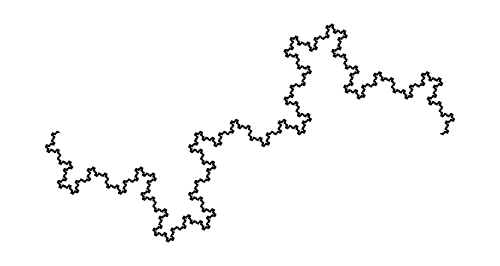

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(x2-x1)/4+(y2-y1)/4,y1-(x2-x1)/4+(y2-y1)/4},{x1+(x2-x1)/2,y1+(y2-y1)/2},{x1+3 (x2-x1)/4-(y2-y1)/4,y1+(x2-x1)/4+3 (y2-y1)/4}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-3];

list=Nest[a2,{{0.,0.},{1.,0.}},6];

Graphics[Line[list],ImageSize->500]
```

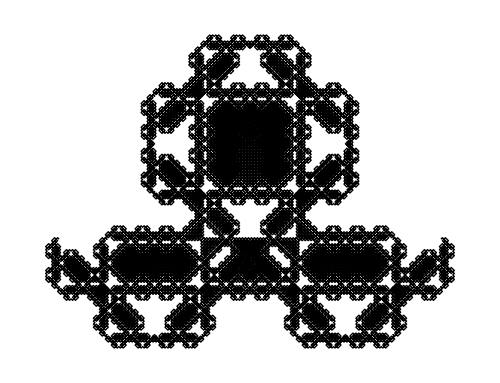

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(x2-x1)/4+(y2-y1)/4,y1-(x2-x1)/4+(y2-y1)/4},{x1+(x2-x1)/2,y1+(y2-y1)/2},{x1+3 (x2-x1)/4-(y2-y1)/4,y1+(x2-x1)/4+3 (y2-y1)/4},{x1+(x2-x1)/2-(y2-y1)/2,y1+(x2-x1)/2+(y2-y1)/2},{x1+(x2-x1)/4-(y2-y1)/4,y1+(x2-x1)/4+(y2-y1)/4},{x1+(x2-x1)/2,y1+(y2-y1)/2},{x1+3 (x2-x1)/4+(y2-y1)/4,y1-(x2-x1)/4+3 (y2-y1)/4}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-7];

list=Nest[a2,{{0.,0.},{1.,0.}},5];

Graphics[Line[list],ImageSize->500]
```

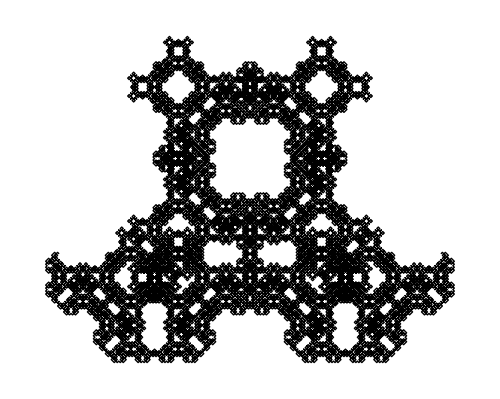

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1+(x2-x1)/4+(y2-y1)/4,y1-(x2-x1)/4+(y2-y1)/4},{x1+(x2-x1)/2,y1+(y2-y1)/2},{x1+(x2-x1)/4-(y2-y1)/4,y1+(x2-x1)/4+(y2-y1)/4},{x1+(x2-x1)/2-(y2-y1)/2,y1+(x2-x1)/2+(y2-y1)/2},{x1+3 (x2-x1)/4-(y2-y1)/4,y1+(x2-x1)/4+3 (y2-y1)/4},{x1+(x2-x1)/2,y1+(y2-y1)/2},{x1+3 (x2-x1)/4+(y2-y1)/4,y1-(x2-x1)/4+3 (y2-y1)/4}};

a2[a_]:=Drop[Join@@a1/@Transpose[{#,RotateLeft[#]}]&[a],-7];

list=Nest[a2,{{0.,0.},{1.,0.}},5];

Graphics[Line[list],ImageSize->500]
```

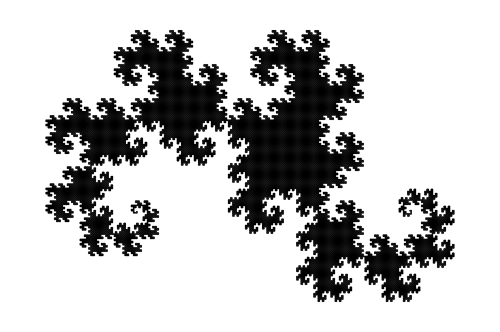

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{{x1,y1},{x1+(x2-x1)/2-(y2-y1)/2,y1+(x2-x1)/2+(y2-y1)/2}},{{x2,y2},{x1+(x2-x1)/2-(y2-y1)/2,y1+(x2-x1)/2+(y2-y1)/2}}};

a2[a_]:=Join@@a1/@a;

list=Nest[a2,{{{0.,0.},{1.,0.}}},15];

Graphics[Line[list],ImageSize->500]
```

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:=If[(x2-x1)^2+(y2-y1)^2<0.00001,{{{x1,y1},{x2,y2}}},{{{x1,y1},{x1+4 (x2-x1)/5-2 (y2-y1)/5,y1+2 (x2-x1)/5+4 (y2-y1)/5}},{{x2,y2},{x1+4 (x2-x1)/5-2 (y2-y1)/5,y1+2 (x2-x1)/5+4 (y2-y1)/5}}}];

a2[a_]:=Join@@a1/@a;

list=Nest[a2,{{{0.,0.},{1.,0.}}},29];

Graphics[Line[list],ImageSize->500]
```

-Graphics-

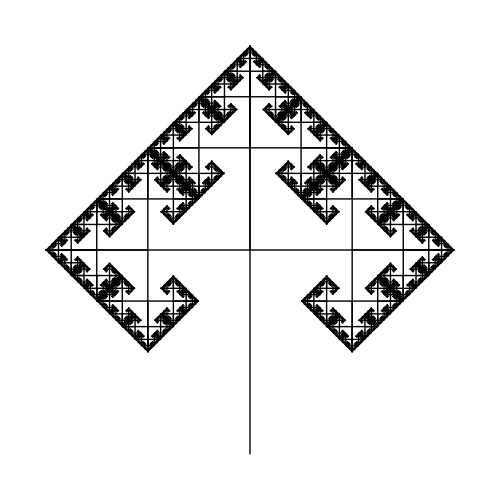

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{{x1+(x2-x1)/2,y1+(y2-y1)/2},{x2,y2}},{{x1+(x2-x1)/2,y1+(y2-y1)/2},{x1+(x2-x1)/2-(y2-y1)/2,y1+(x2-x1)/2+(y2-y1)/2}},{{x1+(x2-x1)/2,y1+(y2-y1)/2},{x1+(x2-x1)/2+(y2-y1)/2,y1-(x2-x1)/2+(y2-y1)/2}}};

a2[a_]:=Join@@a1/@a;

list=Join@@NestList[a2,{{{0.,0.},{0.,1.}}},8];

Graphics[Line[list],ImageSize->500]
```

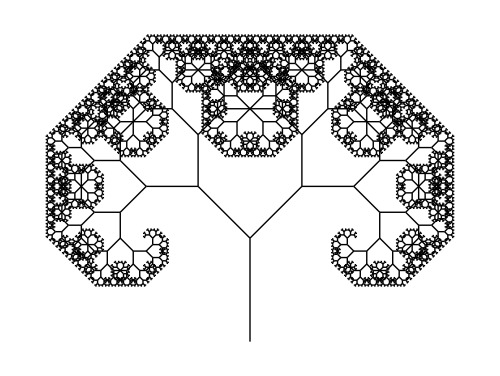

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{{x2,y2},{x2+(x2-x1)/2-(y2-y1)/2,y2+(x2-x1)/2+(y2-y1)/2}},{{x2,y2},{x2+(x2-x1)/2+(y2-y1)/2,y2-(x2-x1)/2+(y2-y1)/2}}};

a2[a_]:=Join@@a1/@a;

list=Join@@NestList[a2,{{{0.,0.},{0.,1.}}},12];

Graphics[Line[list],ImageSize->500]
```

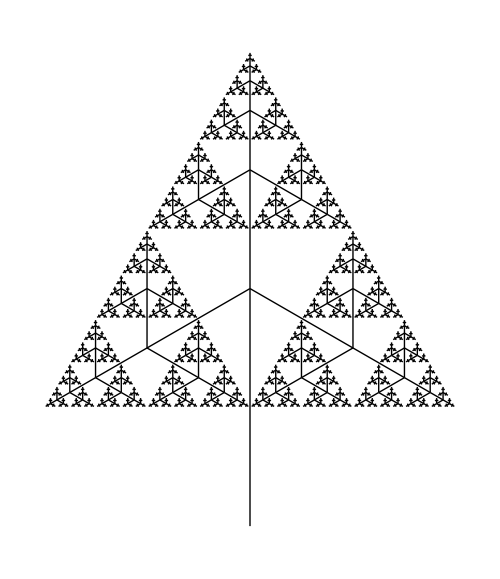

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{{x2,y2},{x2+(x2-x1)/2,y2+(y2-y1)/2}},{{x2,y2},{x2-(x2-x1)/4+Sqrt[3] (y2-y1)/4,y2-Sqrt[3] (x2-x1)/4-(y2-y1)/4}},{{x2,y2},{x2-(x2-x1)/4-Sqrt[3] (y2-y1)/4,y2+Sqrt[3] (x2-x1)/4-(y2-y1)/4}}};

a2[a_]:=Join@@a1/@a;

list=Join@@NestList[a2,{{{0.,0.},{0.,1.}}},7];

Graphics[Line[list],ImageSize->500]
```

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{{x2,y2},{x2+(x2-x1)/2,y2+(y2-y1)/2}},{{x2,y2},{x2-(x2-x1)/4+Sqrt[3] (y2-y1)/4,y2-Sqrt[3] (x2-x1)/4-(y2-y1)/4}},{{x2,y2},{x2-(x2-x1)/4-Sqrt[3] (y2-y1)/4,y2+Sqrt[3] (x2-x1)/4-(y2-y1)/4}},{{x2,y2},{x2+(x2-x1)/4+Sqrt[3] (y2-y1)/4,y2-Sqrt[3] (x2-x1)/4+(y2-y1)/4}},{{x2,y2},{x2+(x2-x1)/4-Sqrt[3] (y2-y1)/4,y2+Sqrt[3] (x2-x1)/4+(y2-y1)/4}}};

a2[a_]:=Join@@a1/@a;

list=Join@@NestList[a2,{{{0.,0.},{0.,1.}}},7];

Graphics[Line[list],ImageSize->500]
```

-Graphics-

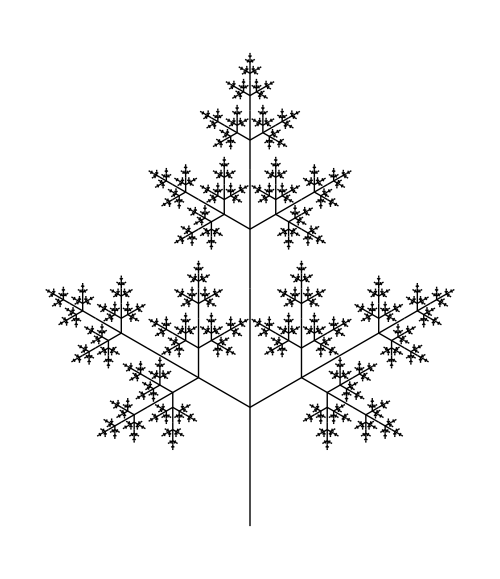

```mathematica
a1[{{x1_,y1_},{x2_,y2_}}]:={{{x2,y2},{x2+(x2-x1)/2,y2+(y2-y1)/2}},{{(x1+x2)/2,(y1+y2)/2},{(x1+x2)/2+(x2-x1)/4+Sqrt[3] (y2-y1)/4,(y1+y2)/2-Sqrt[3] (x2-x1)/4+(y2-y1)/4}},{{(x1+x2)/2,(y1+y2)/2},{(x1+x2)/2+(x2-x1)/4-Sqrt[3] (y2-y1)/4,(y1+y2)/2+Sqrt[3] (x2-x1)/4+(y2-y1)/4}}};

a2[a_]:=Join@@a1/@a;

list=Join@@NestList[a2,{{{0.,0.},{0.,1.}}},7];

Graphics[Line[list],ImageSize->500]
```